```mathematica
t[k_,n_]:=-Cos[(π/2)((2k-1)/n)]
```

```mathematica
ChebyRoots[n_]:=Map[Function[k,t[k,n]],Range[n]]
```

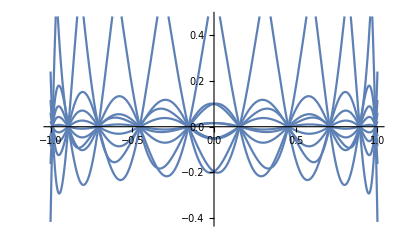

```mathematica
With[{N=10},Plot[Map[Function[n,u[x,n,N]],Range[N]],{x,-1,1}]]
```

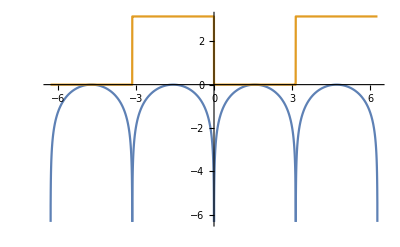

```mathematica
Plot[{Re[Log[Sin[x]]],Im[Log[Sin[x]]]},{x,-2π,2π}]
```

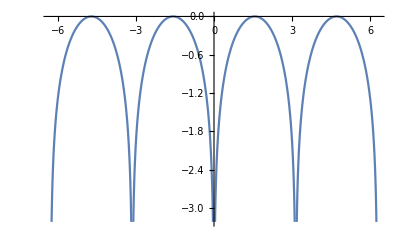

```mathematica
Plot[1/2 Log[Sin[x]^2],{x,-2π,2π}]
```

```mathematica
D[1/2 Log[Sin[x]^2],x]
```

Cot[x]

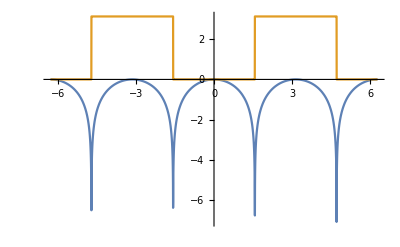

```mathematica
With[{f=Function[x,Log[Cos[x]]]},
Plot[{Re[f[x]],Im[f[x]]},{x,-2π,2π}]]
```

```mathematica
LogCosCoef[n_]:=Piecewise[
{{Undefined,OddQ[n]∨n≤0},
{((-1)^(n/2) 2^(n-1)(2^n-1) BernoulliB[n])/(n/2 Factorial[ n]),EvenQ[n]}},n]
```

```mathematica
LogCosApprox[x_,N_]:=Sum[LogCosCoef[2 n] x^(2 n),{n,N}]
```

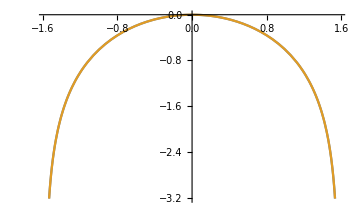

```mathematica
Plot[{LogCosApprox[x,100],Log[Cos[x]]},{x,-π/2,π/2}]
```

```mathematica
Table[LogCosCoef[2n],{n,1,10}]
```

{-1/2,-1/12,-1/45,-17/2520,-31/14175,-691/935550,-10922/42567525,-929569/10216206000,-3202291/97692469875,-221930581/18561569276250}

```mathematica
M=100
```

100

```mathematica
xs=RandomReal[{-π,π},M]
```

{0.143307,-0.638693,-1.32335,-0.717247,-1.90291,0.343448,2.36513,1.4711,-0.660926,1.05982,2.89769,1.1994,0.258334,-2.04012,-1.71519,0.994183,0.755622,-0.873472,2.46715,-1.31594,1.2697,-1.30191,-0.472475,-2.38148,-2.49446,-2.92064,1.3711,-0.425235,-2.55714,1.57885,-0.933156,0.00642248,-2.74639,-2.9594,-2.84649,2.48648,1.35815,-2.3777,1.15946,0.296952,2.13932,2.29597,-3.06106,2.01335,-3.09133,0.781542,-2.51336,-0.955085,1.30486,1.03082,1.557,-1.18676,-1.72591,-0.213044,-1.687,1.57675,-0.499947,1.41891,-2.81357,0.19202,-1.22852,-1.64813,2.72616,-0.32677,2.134,2.57194,0.388918,0.452494,-2.3101,1.9684,0.0534482,1.34631,2.82446,-3.1047,0.209358,-0.472004,2.2482,0.0705756,-1.57596,-2.36023,-1.9012,1.67473,3.11276,1.45203,1.38586,2.05471,-2.02542,-0.305809,-1.50448,-2.2855,-1.80753,1.93143,-0.144466,0.567509,2.53318,-0.340897,-0.0402757,-0.360941,2.9509,2.89497}

```mathematica
ys=RandomReal[{-π,π},M]
```

{0.761915,-2.18009,2.92086,-0.911826,-1.57497,-1.59638,-2.5613,0.936187,0.0972016,1.24038,-2.39913,2.45773,-2.40393,1.71279,0.570792,0.912725,1.34433,2.81044,0.299891,3.03246,-1.15501,2.45081,1.72515,2.70783,-2.78576,-0.499973,-0.657861,1.01821,-3.00135,-2.72862,1.39819,1.1769,-1.29855,-1.86055,-3.14051,2.62946,2.75291,0.436931,-2.62399,-3.01449,2.39328,1.47382,3.01138,1.65004,2.75197,-0.861551,-2.36792,3.03323,0.0694855,2.56498,0.954519,-2.62522,2.81521,-0.885983,-2.76872,0.101641,2.02745,0.385966,-1.95291,-2.84399,-1.23202,2.04198,0.777155,-1.12985,-0.0798177,0.749552,1.75734,-0.928451,0.857171,-2.77065,1.77437,2.11785,2.05676,-0.960228,2.93636,-2.63873,0.474533,-2.48921,1.8846,1.0507,1.09125,0.388757,-2.09283,-0.533021,-2.64695,1.03642,1.4916,0.00444257,-2.07978,-2.00449,1.60088,0.935158,1.12902,-0.558894,2.83659,2.83607,-0.26195,-0.22345,1.14165,2.55245}

```mathematica
diffs=Apply[Function[{x,y},(x-y)/2],Tuples[{xs,ys}],{1}]
```

{-0.309304,1.1617,-1.38877,0.527567,0.859138,0.869843,1.3523,-0.39644,0.023053,-0.548534,1.27122,-1.15721,1.27362,-0.78474,-0.213742,9970,0.929274,0.701682,1.44526,2.48737,2.44973,0.647042,0.979905,0.882975,1.72693,0.029189,0.0294495,1.57846,1.55921,0.876658,0.17126}
 |  |  |  |

```mathematica
{Apply[Max,diffs],Apply[Min,diffs]}
```

{3.12663,-3.06897}

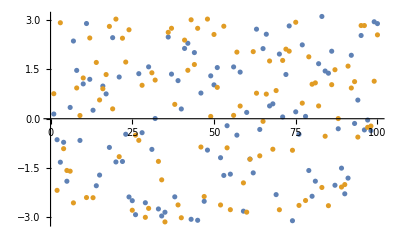

```mathematica
ListPlot[{xs,ys}]
```

```mathematica
c1[l_]:=Product[Sin[(xs[[l]]-ys[[k]])/2],{k,M}]
```

```mathematica
c1table=Table[c1[l],{l,M}]
```

{-4.77754×10^-28,-9.83321×10^-25,-3.45443×10^-23,4.72459×10^-24,2.86948×10^-25,7.61826×10^-30,1.31094×10^-32,-9.03254×10^-36,2.20184×10^-25,1.49797×10^-38,-2.58171×10^-37,3.14745×10^-36,-2.50847×10^-28,2.90419×10^-27,-7.13424×10^-23,-7.67397×10^-38,1.15052×10^-35,-8.47343×10^-27,-4.58051×10^-35,-2.08632×10^-23,-5.52724×10^-35,-2.88807×10^-24,9.38551×10^-25,1.0827×10^-31,-7.71804×10^-33,-5.33758×10^-33,8.11775×10^-35,4.32078×10^-24,-4.30395×10^-34,-2.53097×10^-34,2.97647×10^-27,1.60851×10^-28,-8.80938×10^-36,-3.42123×10^-33,-5.49263×10^-35,-1.51837×10^-34,5.75674×10^-35,1.26879×10^-31,-1.99818×10^-37,-5.94441×10^-30,2.79524×10^-32,2.03595×10^-31,-1.97169×10^-33,1.14737×10^-33,-1.75026×10^-33,1.09918×10^-35,-1.51671×10^-32,1.11155×10^-26,-1.2261×10^-34,4.15551×10^-39,-4.36958×10^-34,-2.22924×10^-24,-6.43163×10^-23,7.41047×10^-26,-7.95474×10^-23,-2.77746×10^-34,3.58883×10^-28,-1.07772×10^-34,8.0403×10^-35,-1.03905×10^-27,-6.69545×10^-25,-5.64316×10^-23,-1.42979×10^-37,2.8999×10^-24,1.80894×10^-32,-3.98826×10^-36,6.74723×10^-34,-1.91248×10^-31,-6.26553×10^-29,1.19672×10^-32,1.9859×10^-28,9.32544×10^-36,-7.92931×10^-40,-1.23185×10^-33,-9.21192×10^-28,9.64362×10^-25,3.50575×10^-31,-5.9036×10^-30,5.92237×10^-25,-5.34607×10^-31,3.01231×10^-25,-6.30927×10^-35,2.07539×10^-34,-9.55028×10^-35,5.65847×10^-35,5.1215×10^-35,3.44367×10^-27,1.52731×10^-24,-1.96584×10^-22,-1.96323×10^-28,-9.21443×10^-24,1.24638×10^-32,1.85975×10^-25,7.51527×10^-32,-3.73729×10^-35,3.89209×10^-24,-9.3287×10^-27,5.10003×10^-24,-4.69214×10^-37,-2.66393×10^-37}

```mathematica
c2[l_]:=Re[Exp[Sum[Log[Sin[(xs[[l]]-ys[[k]])/2]],{k,M}]]]
```

```mathematica
c2table=Table[c2[l],{l,M}]
```

{-4.77754×10^-28,-9.83321×10^-25,-3.45443×10^-23,4.72459×10^-24,2.86948×10^-25,7.61826×10^-30,1.31094×10^-32,-9.03254×10^-36,2.20184×10^-25,1.49797×10^-38,-2.58171×10^-37,3.14745×10^-36,-2.50847×10^-28,2.90419×10^-27,-7.13424×10^-23,-7.67397×10^-38,1.15052×10^-35,-8.47343×10^-27,-4.58051×10^-35,-2.08632×10^-23,-5.52724×10^-35,-2.88807×10^-24,9.38551×10^-25,1.0827×10^-31,-7.71804×10^-33,-5.33758×10^-33,8.11775×10^-35,4.32078×10^-24,-4.30395×10^-34,-2.53097×10^-34,2.97647×10^-27,1.60851×10^-28,-8.80938×10^-36,-3.42123×10^-33,-5.49263×10^-35,-1.51837×10^-34,5.75674×10^-35,1.26879×10^-31,-1.99818×10^-37,-5.94441×10^-30,2.79524×10^-32,2.03595×10^-31,-1.97169×10^-33,1.14737×10^-33,-1.75026×10^-33,1.09918×10^-35,-1.51671×10^-32,1.11155×10^-26,-1.2261×10^-34,4.15551×10^-39,-4.36958×10^-34,-2.22924×10^-24,-6.43163×10^-23,7.41047×10^-26,-7.95474×10^-23,-2.77746×10^-34,3.58883×10^-28,-1.07772×10^-34,8.0403×10^-35,-1.03905×10^-27,-6.69545×10^-25,-5.64316×10^-23,-1.42979×10^-37,2.8999×10^-24,1.80894×10^-32,-3.98826×10^-36,6.74723×10^-34,-1.91248×10^-31,-6.26553×10^-29,1.19672×10^-32,1.9859×10^-28,9.32544×10^-36,-7.92931×10^-40,-1.23185×10^-33,-9.21192×10^-28,9.64362×10^-25,3.50575×10^-31,-5.9036×10^-30,5.92237×10^-25,-5.34607×10^-31,3.01231×10^-25,-6.30927×10^-35,2.07539×10^-34,-9.55028×10^-35,5.65847×10^-35,5.1215×10^-35,3.44367×10^-27,1.52731×10^-24,-1.96584×10^-22,-1.96323×10^-28,-9.21443×10^-24,1.24638×10^-32,1.85975×10^-25,7.51527×10^-32,-3.73729×10^-35,3.89209×10^-24,-9.3287×10^-27,5.10003×10^-24,-4.69214×10^-37,-2.66393×10^-37}

```mathematica
Log[Sin[(xs[[5]]-ys[[8]])/2]]
```

-0.0114818+3.14159 ⅈ

```mathematica
T=Function[δ,Piecewise[{{δ-π/2,δ>0},{δ+π/2,δ<0},{0,δ==0}},δ]]
```

Function[δ,Piecewise[{{δ-π/2, δ>0}, {δ+π/2, δ<0}, {0, δ==0}, {δ, True}}]]

```mathematica
c3[l_]:=With[{x=xs[[l]]},
Exp[Sum[With[{y=ys[[k]]-If[x>ys[[k]],π,-π]},Cos[(x-y)/2]],{k,M}]]]
```

```mathematica
c3table=Table[c3[l],{l,M}]
```

{2.51011×10^-29,6.90849×10^-31,3.84397×10^-31,5.80943×10^-31,3.27496×10^-30,9.86869×10^-29,2.60828×10^-26,2.2849×10^-26,6.59672×10^-31,1.22569×10^-26,2.77356×10^-26,1.61207×10^-26,5.21956×10^-29,8.7009×10^-30,1.05598×10^-30,9.32913×10^-27,1.95982×10^-27,5.3878×10^-31,3.14133×10^-26,3.85098×10^-31,1.72449×10^-26,3.87447×10^-31,1.05069×10^-30,1.17742×10^-28,2.90311×10^-28,3.31002×10^-27,1.98449×10^-26,1.17773×10^-30,4.81563×10^-28,2.51427×10^-26,5.1515×10^-31,1.0877×10^-29,1.6767×10^-27,3.93731×10^-27,2.53145×10^-27,3.18355×10^-26,1.95125×10^-26,1.13914×10^-28,1.5493×10^-26,7.00502×10^-29,2.39189×10^-26,2.34489×10^-26,6.21972×10^-27,2.61154×10^-26,7.13612×10^-27,2.3774×10^-27,3.35977×10^-28,4.95065×10^-31,1.79615×10^-26,1.10932×10^-26,2.44354×10^-26,3.96482×10^-31,1.11098×10^-30,2.97358×10^-30,9.32799×10^-31,2.50661×10^-26,1.00077×10^-30,2.11372×10^-26,2.23957×10^-27,3.33308×10^-29,3.93078×10^-31,8.04065×10^-31,3.7759×10^-26,1.69045×10^-30,2.40877×10^-26,3.51223×10^-26,1.4186×10^-28,2.16896×10^-28,6.1893×10^-29,2.55×10^-26,1.47972×10^-29,1.92554×10^-26,3.5462×10^-26,7.61599×10^-27,3.72185×10^-29,1.05169×10^-30,2.27028×10^-26,1.66861×10^-29,6.40968×10^-31,9.73151×10^-29,3.23683×10^-30,2.80599×10^-26,1.0584×10^-26,2.21047×10^-26,2.02915×10^-26,2.63312×10^-26,7.84445×10^-30,1.86528×10^-30,4.95698×10^-31,5.03106×10^-29,1.74483×10^-30,2.55688×10^-26,4.20095×10^-30,4.59874×10^-28,3.36314×10^-26,1.58869×10^-30,7.94684×10^-30,1.46331×10^-30,2.29151×10^-26,2.79756×10^-26}

```mathematica
test[l_,k_]:=With[
{x=xs[[l]],y=ys[[k]]},
Log[Cos[(x-(y-If[(x-y)/2<0,π,-π]))/2]]]
```

```mathematica
c3[l_]:=Exp[Sum[test[l,k],{k,M}]]
```

```mathematica
c3table=Table[c3[l],{l,M}]
```

{4.77754×10^-28,9.83321×10^-25,3.45443×10^-23,4.72459×10^-24,2.86948×10^-25,7.61826×10^-30,1.31094×10^-32,9.03254×10^-36,2.20184×10^-25,1.49797×10^-38,2.58171×10^-37,3.14745×10^-36,2.50847×10^-28,2.90419×10^-27,7.13424×10^-23,7.67397×10^-38,1.15052×10^-35,8.47343×10^-27,4.58051×10^-35,2.08632×10^-23,5.52724×10^-35,2.88807×10^-24,9.38551×10^-25,1.0827×10^-31,7.71804×10^-33,5.33758×10^-33,8.11775×10^-35,4.32078×10^-24,4.30395×10^-34,2.53097×10^-34,2.97647×10^-27,1.60851×10^-28,8.80938×10^-36,3.42123×10^-33,5.49263×10^-35,1.51837×10^-34,5.75674×10^-35,1.26879×10^-31,1.99818×10^-37,5.94441×10^-30,2.79524×10^-32,2.03595×10^-31,1.97169×10^-33,1.14737×10^-33,1.75026×10^-33,1.09918×10^-35,1.51671×10^-32,1.11155×10^-26,1.2261×10^-34,4.15551×10^-39,4.36958×10^-34,2.22924×10^-24,6.43163×10^-23,7.41047×10^-26,7.95474×10^-23,2.77746×10^-34,3.58883×10^-28,1.07772×10^-34,8.0403×10^-35,1.03905×10^-27,6.69545×10^-25,5.64316×10^-23,1.42979×10^-37,2.8999×10^-24,1.80894×10^-32,3.98826×10^-36,6.74723×10^-34,1.91248×10^-31,6.26553×10^-29,1.19672×10^-32,1.9859×10^-28,9.32544×10^-36,7.92931×10^-40,1.23185×10^-33,9.21192×10^-28,9.64362×10^-25,3.50575×10^-31,5.9036×10^-30,5.92237×10^-25,5.34607×10^-31,3.01231×10^-25,6.30927×10^-35,2.07539×10^-34,9.55028×10^-35,5.65847×10^-35,5.1215×10^-35,3.44367×10^-27,1.52731×10^-24,1.96584×10^-22,1.96323×10^-28,9.21443×10^-24,1.24638×10^-32,1.85975×10^-25,7.51527×10^-32,3.73729×10^-35,3.89209×10^-24,9.3287×10^-27,5.10003×10^-24,4.69214×10^-37,2.66393×10^-37}